# AD Faked QN+ From Scratch

## The CUTER Rosenbrock is not what I thought.

The cuter generalized Rosenbrock is not what everyone else uses!  The two recipes are below.

```mathematica
Clear[CRosen, Rosen]
CRosen[a_][x_List]:= Module[{n=Length[x]},
1+Sum[a(x⟦i⟧-x⟦i-1⟧^2)^2,{i,2, n}]+Sum[(x⟦i⟧-1)^2,{i,2, n}]]
Rosen[a_][x_List]:= Sum[a*(x⟦i+1⟧-x⟦i⟧^2)^2+(1-x⟦i⟧)^2,{i, Length[x]-1}]
```

The critical point structures are NOT similar!  I set up the derivatives semi-manually and checked against a fixed dimensional automated versions.

### Derivatives

```mathematica
Clear[dRosen,dCRosen,ddRosen,ddCRosen]
dRosen[a_][x_List]:= Module[{n=Length[x]},
Join[
{-2*(1-x⟦1⟧)-4*a *x⟦1⟧ (-x⟦1⟧^2+x⟦2⟧)},
Table[ -2*(1-x⟦i⟧)+2*a (-x⟦-1+i⟧^2+x⟦i⟧)-4*a x⟦i⟧ (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*a(x⟦n⟧-x⟦n-1⟧^2)}]
]
ddRosen[a_][x_List]:=Module[{n=Length[x],MainDiagonal,OffDiagonal},
MainDiagonal=Join[
{2+8*a x⟦1⟧^2-4*a (-x⟦1⟧^2+x⟦2⟧)},
Table[2*a+2+8*a x⟦i⟧^2-4*a (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*a}];
OffDiagonal=-4*a*x⟦1;;n-1⟧;
SparseArray[{
Band[{1,2}]->OffDiagonal,
Band[{2,1}]->OffDiagonal,
Band[{1,1}]->MainDiagonal
},{n,n}]
]
dCRosen[a_][x_List]:= Module[{n=Length[x]},
Join[
{-4*a*x⟦1⟧ (-x⟦1⟧^2+x⟦2⟧)},
Table[ 2 (-1+x⟦i⟧)+2*a (-x⟦-1+i⟧^2+x⟦i⟧)-4*a x⟦i⟧ (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*(-1+x⟦n⟧)+2*a (-x⟦n-1⟧^2+x⟦n⟧)}]
]
ddCRosen[a_][x_List]:=Module[{n=Length[x],MainDiagonal,OffDiagonal},
MainDiagonal=Join[
{8*a*x⟦1⟧^2-4*a (-x⟦1⟧^2+x⟦2⟧)},
Table[2*a+2+8*a *x⟦i⟧^2-4*a (-x⟦i⟧^2+x⟦1+i⟧),{i,2,n-1}],
{2*a+2}];
OffDiagonal=-4*a*x⟦1;;n-1⟧;
SparseArray[{
Band[{1,2}]->OffDiagonal,
Band[{2,1}]->OffDiagonal,
Band[{1,1}]->MainDiagonal
},{n,n}]
]
```

Testing the first and second derivatives

```mathematica
n=123;
x0=RandomReal[{-1,1},n];
x0Sub = Table[Symbol[StringJoin["$x",ToString[i]]]->x0⟦i⟧,{i,n}];
vars=x0Sub⟦All,1⟧;
a = 10;
Map[Norm,{dRosen[a][x0]-D[ Rosen[a][vars],{vars}]/.x0Sub,
dCRosen[a][x0]-D[ CRosen[a][vars],{vars}]/.x0Sub}]
Map[Norm,{ddRosen[a][x0]-D[ Rosen[a][vars],{vars,2}]/.x0Sub,
ddCRosen[a][x0]-D[ CRosen[a][vars],{vars,2}]/.x0Sub}]
```

{3.02046×10^-14,3.02054×10^-14}

{1.42109×10^-14,1.42109×10^-14}

#### Some symbolic tools

Some tools I used are below

```mathematica
n=5;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
SymDRosen= D[ Rosen[vars],{vars,2}]//MatrixForm
```

(2+800 ($x1)^2-400 (-($x1)^2+$x2) | -400 $x1 | 0 | 0 | 0
-400 $x1 | 202+800 ($x2)^2-400 (-($x2)^2+$x3) | -400 $x2 | 0 | 0
0 | -400 $x2 | 202+800 ($x3)^2-400 (-($x3)^2+$x4) | -400 $x3 | 0
0 | 0 | -400 $x3 | 202+800 ($x4)^2-400 (-($x4)^2+$x5) | -400 $x4
0 | 0 | 0 | -400 $x4 | 200)

```mathematica
n=6;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
SymDRosen= D[ Rosen[vars],{vars}];
SymDCRosen= D[ CRosen[vars],{vars}];

Quiet[
SymDRosen[[1]]/.{vars⟦1⟧->x⟦1⟧, vars⟦2⟧->x⟦2⟧};
SymDRosen⟦2⟧/.{vars⟦1⟧->x⟦i-1⟧, vars⟦2⟧->x⟦i⟧,vars⟦3⟧->x⟦i+1⟧};
SymDRosen[[n]]
]

Quiet[
SymDCRosen[[1]]/.{vars⟦1⟧->x⟦1⟧, vars⟦2⟧->x⟦2⟧};
SymDCRosen⟦2⟧/.{vars⟦1⟧->x⟦i-1⟧, vars⟦2⟧->x⟦i⟧,vars⟦3⟧->x⟦i+1⟧};
SymDCRosen[[n]];
]
```

200 (-($x5)^2+$x6)

```mathematica
dRosenTest =Function[Evaluate[vars],Evaluate[D[Rosen[vars],{vars}]]];
x0=RandomReal[{-1,1},n];
{dRosen[x0],Apply[dRosenTest,x0]}
```

{{-33.7413,23.175,-70.3565,209.891,-119.833,0},{-39.275,-28.7982,43.281,269.342,-287.23,-156.616}}

```mathematica
D[Rosen[vars],{vars}][[2]]
```

-2 (1-$x2)+200 (-($x1)^2+$x2)-400 $x2 (-($x2)^2+$x3)

```mathematica
dCRosen =Function[Evaluate[vars],Evaluate[D[CRosen[vars],{vars}]]];
ddRosen =Function[Evaluate[vars],Evaluate[D[Rosen[vars],{vars,2}]]];
ddCRosen =Function[Evaluate[vars],Evaluate[D[CRosen[vars],{vars,2}]]];
dRC[x_]:= Apply[dCRosen,x]
dR[x_]:=Apply[dRosen,x]
```

Even in low dimensions there are striking differences.

```mathematica
v0=RandomReal[{-1,1},n];
FindRoot[dRC[vars]==0,{vars,v0}ᵀ,MaxIterations->10^3]
```

```mathematica
Hmm=vars/.{$x1->-1.,$x2->1.,$x3->1.,$x4->1.,$x5->1.,$x6->1.}
Eigenvalues[Apply[ddCRosen,Hmm]]
CRosen[Hmm]
CRosen[ConstantArray[1,n]]
```

{-1.,1.,1.,1.,1.,1.}

{1694.74,1401.71,1001.47,601.333,308.744,1.99853}

1.

1.

```mathematica
Hmm=vars/.{$x1->1.6463417388458558*^-15,$x2->0.010103136618591437,$x3->0.01020626142941585,$x4->0.01020829236306247,$x5->0.010204209653884877,$x6->0.010004085044218255}
```

{1.64634×10^-15,0.0101031,0.0102063,0.0102083,0.0102042,0.0100041}

```mathematica
Norm[Eigenvalues[Apply[ddCRosen,Hmm]]
```

{205.853,203.331,199.178,194.686,191.201,-4.04125}

### Critical Points and Characterizations

#### Duplicate Global Minima

The first observation is that CRosen has duplicate double global minima of 0 at
	(±1,1,1,1,…,1)

```mathematica
n=10;
xp=xm=ConstantArray[1,n];xm⟦1⟧=-1;
Map[Rosen,{xp,xm}]
Map[CRosen,{xp,xm}]
```

{0,4}

{1,1}

#### CP search

To keep this speedy I am not making it take more steps. First an assessment of the easiness of finding CPs,  I am going to run FindRoot out of the box and on the same ICs see how often it succeeds in finding a CP.  Finding CPs is way easier with the CUTER Rosenbrock!

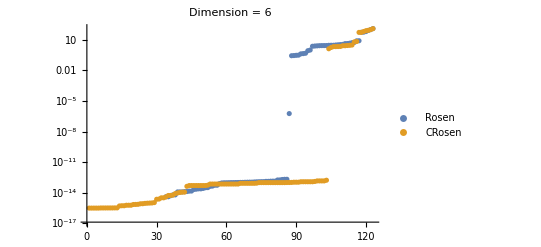

```mathematica
n=6; 
Samples=123;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

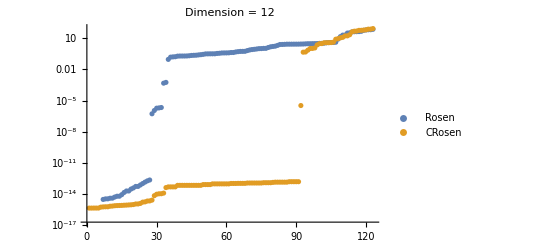

```mathematica
n=12; 
Samples=123;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

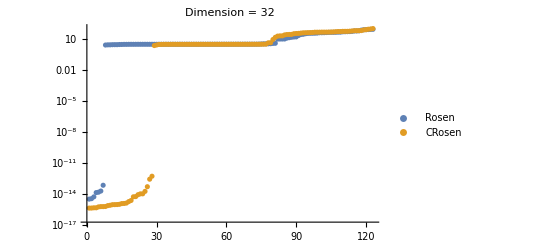

```mathematica
n=32; 
Samples=123;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

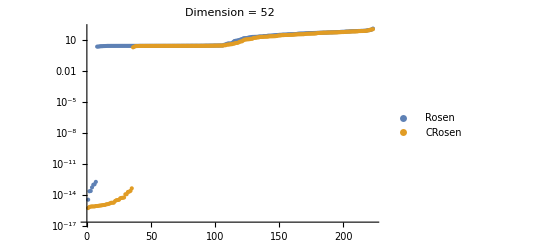

```mathematica
n=52; 
Samples=223;
{RosenResiduals,CRosenResiduals}=Table[
x0=RandomReal[{-1.2,1.2},n];
Quiet[{CPR,CPCR}=x/.Map[FindRoot[ #[x],{x,x0}]&,{dRosen,dCRosen}];];
Map[Norm,{dRosen[CPR],dCRosen[CPCR]}],
{Samples}]ᵀ;
ListLogPlot[Map[Sort,{RosenResiduals,CRosenResiduals}],
PlotLegends->{"Rosen","CRosen"},
PlotLabel->StringForm["Dimension = ``",n]]
```

#### CP Classification search

The plan now is to automate the search for as many types of CPs as I can find for CRosen.  I know the CP structure for Rosenbrock.  So I am focusing on the variant. I can probably do the computation up to n=7 or 8.  All the way up to 7 there are the two matched global minima and a single saddle.

```mathematica
n=4;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=N[vars/.Solve[ dRosen[vars]==0.0,vars, Reals]];
TableForm[
Map[Eigenvalues[ddRosen[#]]&,CPs],
TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4
1 | 1567.62 | 1001.8 | 436.085 | 0.492959
2 | 866.127 | 440.433 | 190.813 | 0.379534
3 | 653.999 | 310.353 | 168.865 | -0.5687

```mathematica
n=7;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=N[vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]];
TableForm[
Map[Eigenvalues[ddCRosen[#]]&,CPs],
TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7
1 | 1722.73 | 1500.61 | 1179.65 | 823.455 | 502.65 | 280.915 | 1.99963
2 | 205.952 | 204.108 | 200.897 | 197.063 | 193.439 | 190.83 | -4.04125
3 | 1722.73 | 1500.61 | 1179.65 | 823.455 | 502.65 | 280.915 | 1.99963

| 1 | 2 | 3 | 4 | 5 | 6
1 | 1694.74 | 1401.71 | 1001.47 | 601.333 | 308.744 | 1.99853
2 | 205.853 | 203.331 | 199.178 | 194.686 | 191.201 | -4.04125
3 | 1694.74 | 1401.71 | 1001.47 | 601.333 | 308.744 | 1.99853

The single saddle is at {,…,} and the single negative eigenvalue looks to always be the same value of

There is a saddle in 2 dimensions. separating the two minima.

```mathematica
n=2;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]
```

{{-1,1},{0,1/101},{1,1}}

The first non-trivial value for the saddle is the root of a cubic for n=3!

```mathematica
n=3;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]
Normal[CPs⟦2,2,1⟧][x]
```

{{-1,1,1},{0,Root0.0101Root[-101+10001 #1+200 #1^3&,1]0.01009896950333628,Root0.0100Root[{-101+10001 #1+200 #1^3&,1+100 #1^2-101 #2&},{1,1}]0.010001969490128037},{1,1,1}}

-101+10001 x+200 x^3

```mathematica
n=4;
vars=Table[Symbol[StringJoin["$x",ToString[i]]],{i,n}];
CPs=vars/.Solve[ dCRosen[vars]==0.0,vars, Reals]
Normal[CPs⟦2,2,1⟧][x]
N[CPs]
```

{{-1,1,1,1},{0,Root0.0101Root[-1+303 #1-2030803 #1^2+199011101 #1^3-121200 #1^4+2160600 #1^5-120000 #1^6+12120000 #1^7+8000000 #1^9&,1]0.010103050698337002,Root0.0102Root[{-1+303 #1-2030803 #1^2+199011101 #1^3-121200 #1^4+2160600 #1^5-120000 #1^6+12120000 #1^7+8000000 #1^9&,202-2030803 #1+199010901 #1^2-121200 #1^3+2160600 #1^4-120000 #1^5+12120000 #1^6+8000000 #1^8+200 #2&},{1,1}]0.010202050907691369,Root0.0100Root[{-1+303 #1-2030803 #1^2+199011101 #1^3-121200 #1^4+2160600 #1^5-120000 #1^6+12120000 #1^7+8000000 #1^9&,-1989599-6100402 #1+20100040401 #1^2-10080600 #1^3+218140600 #1^4+1224120000 #1^6+8000000 #1^7+808000000 #1^8-40400 #2&},{1,1}]0.01000404142843874},{1,1,1,1}}

-1+303 x-2030803 x^2+199011101 x^3-121200 x^4+2160600 x^5-120000 x^6+12120000 x^7+8000000 x^9

{{-1.,1.,1.,1.},{0.,0.0101031,0.0102021,0.010004},{1.,1.,1.,1.}}

#### Pics

The do not even look alike for n=2;

```mathematica
TabView[{
"Rosen"->ContourPlot[ Rosen[{x1,x2}], {x1,-1.8,1.8},{x2,-1.2,1.2},
PlotPoints->20,
PlotRange->{0,10},
Contours->30],
"CRosen"->ContourPlot[CRosen[{x1,x2}], {x1,-1.8,1.8},{x2,-1.2,1.2},
PlotPoints->20,
PlotRange->{0,10},
Contours->30]}]
```

12

I do not think that there is going to be any interesting CPs for the CRosen.  If there are they are hard to find.

I will try to do this a bit later.

## Code

### Options etc

```mathematica
SetOptions[MatrixPlot, PlotLegends->Automatic, AspectRatio->1];
```

### Orthogonalization and Random Generators

```mathematica
Orth[A_]:=Transpose[Orthogonalize[Transpose[A]]]
RandOrth[{m_,n_}]:= Orth[RandomReal[{-1,1},{m,n}]]
RandSym[λs_]:= Module[{m=Length[λs],Q},
Q=RandOrth[{m,m}];
Q.DiagonalMatrix[λs].Qᵀ]
```

To make a random SPD specify positive eigenvalues.

```mathematica
dist=MixtureDistribution[{0.25,0.75},{NormalDistribution[2,1],NormalDistribution[10,1]}];
λs=Sort[RandomVariate[dist,m]];
A= RandSym[λs];
Norm[λs-Sort[Eigenvalues[A]]]
```

1.35575×10^-14

### QN Updates

```mathematica
bSR1[H_,U_,V_,δ_]:= Module[{UMinusHV=U-H.V},
H+ UMinusHV.PseudoInverse[UMinusHVᵀ.V,Tolerance->δ].UMinusHVᵀ
]
bPSB[H_,U_,V_,δ_]:= Module[{T1=PseudoInverse[Vᵀ.V], T2},
T2=V.T1.(U-H.V)ᵀ;
H+T2 + T2ᵀ-T2.V.T1.Vᵀ
]
```

Testing on little guys.  The updates work fine with non-orthogonal inputs U. We are orthogonalizing for convenience and because it seems like the right thing to do.

```mathematica
{n,w,δ}={231,16,1.0*10^-6};
dist=MixtureDistribution[{0.5,0.5},{NormalDistribution[-2,1],NormalDistribution[2,1]}];
λs=Sort[RandomVariate[dist,n]];
A= RandSym[λs]; 
H=RandSym[RandomReal[{-1,1},n]];
U=RandomReal[{-1,1},{n,w}];V=A.U;
{Hs,Hp}=Map[#[H,U,V,δ]&,{bSR1,bPSB}];
(* Test for Symmetry *)
Map[Norm[#-#ᵀ]&,{Hs,Hp}]
(* Test Secant Condition *)
Map[Norm[#.V-U]&,{Hs,Hp}]
```

{2.00373×10^-13,8.27184×10^-16}

{5.01511×10^-13,3.93442×10^-14}

### gHS

The plan is to fake the AD update in the paper Alg4.1.  Since I am faking AD it needs  df and ddf.  I am matching the output format for clarity.

```mathematica
gHSFake[df_,ddf_][{x_,S_}]:= Module[{g=df[x],J=ddf[x],Y},
Y = J.S;
{g, J.g, Y}]
```

Testing a bit.  OK one of the thing to realize is that I made S unit sized so Y is average eigenvalue sized.  However, the gradient g could well be very large or very small with correspondingly sized output h=J.g.  I do not want to mess with gHS but I am going to scale this portion of the input to the QN update.

```mathematica
SetOptions[MatrixPlot, PlotLegends->Automatic,AspectRatio->1];
{n,w}={37,4};
x0=RandomReal[{-1,1},n];
S=RandOrth[{n,2*w-1}];
{g,h,Y}=gHSFake[dRosen,ddRosen][{x0,S}];
Sg = ArrayFlatten[{{S,{g}ᵀ}}];
Yh = ArrayFlatten[{{Y,{h}ᵀ}}];
J = ddRosen[x0];
TabView[{
"S"->MatrixPlot[S],
"Y"->MatrixPlot[Y],
"J.S" ->MatrixPlot[J.S],
"Sg"->MatrixPlot[Sg],
"Yh"->MatrixPlot[Yh],
"J.Sg" ->MatrixPlot[J.Sg]}]
```

123456

### NEW: Initializing H using Hessian Samples

The Hessian sample Y_0=∇^2 f(x_0)S_0 with S_0 provides a conservative and consistent estimate for H_0.  Remember H^-1≈∇^2 f(x).  Estimate is α Id.

```mathematica
αFromgHS[S_,Y_]:= Module[ {λs,n=Length[S],α},
λs =Eigenvalues[Sᵀ.Y] ;  (* SᵀY=Sᵀ∇^2 f(Subscript[x, 0])S and S is orthogonal *)
(* H0 estimate is α Id *)
(* It would also be consistent to use *)
(* α = 1/Mean[λs]; I do not have a preference and do not expect any difference in performance *)
α = Mean[1/λs]
]
```

### U,V input for QN from gHS output

The output from gHS  is {g,h,Y} from input {x,S} where g=∇f(x), h=∇^2 f(x).g, and Y=∇^2 f(x).S.  I am orthogonalizing S so Y gives eigenvalue estimates.  However g is not normalized.  Before I put this into the QN update I am going to normalize g.

```mathematica
BuildUVFromgHSOutput[{g_,h_,Y_},S_]:= Module[{gNorm =Norm[g]},
{ArrayFlatten[{{S,{g}ᵀ/gNorm}}],ArrayFlatten[{{Y,{h}ᵀ/gNorm}}]}]
```

```mathematica
{n,w}={37,4};
x0=RandomReal[{-1,1},n];
S=RandOrth[{n,2*w-1}];
{g,h,Y}=gHSFake[dRosen,ddRosen][{x0,S}];
{U,V}=BuildUVFromgHSOutput[{g,h,Y},S];
J = ddRosen[x0];
Norm[V-J.U,"Frobenius"]
TabView[{
"U"->MatrixPlot[U],
"V"->MatrixPlot[V],
"J.U" ->MatrixPlot[J.U]}]
```

1.25519×10^-13

123

### TRS

Direct implementation of the GEV trust region sub solve using the  algorithm from 
“Solving the Trust Region Sub Problem by a Generalized Eigenvalue Problem”
S. Adachi, S. Iwata, Y. Nakatsukasa, and A. Takeda.    SIAM 2017

Use their notation etc. minimizes 
	0.5 p.A.p+g.p
for 
	p.B.p≤Δ^2
Where A and B are sym. B is SPD and Δ (the trust region radius) is positive.  The underlying dimension is n.  I am mimicking the input and output formats of the Julia TRS implementation from https://github.com/oxfordcontrol/TRS.jl
	(p,info)←trs(A,q,Δ,B;kwargs)
The arguments do not have the same names: A↔P, B↔C.  The main body of our algorithm aligns with the TRS usage because it was less confusing for Dan.  I am not doing the info and keyword args right now.  The algorithm is pretty simple.  It is just one of the standard linearizations of the QEP that you get when you write the Lagrange multiplier form.

```mathematica
TRS[A_,g_,Δ_,B_]:= Module[{n=Length[A],CP,M0,M1,λs,vs,
GapIndex,MaxIndex,λMax,vMax,gap,τ,y1,y2},
(* Compute Critical point *)
CP = LinearSolve[A,-g];
If[ 
(* Test if CP is internal and CP is a min i.e. A is SPD. *)
 And[CP.B.CP ≤Δ^2, Min[Eigenvalues[A]]≥0],CP,
(* return interior min if appropriate otherwise *)
(* Doing the smaller matrix pencil 3.2 *)
{M0,M1} = Map[ArrayFlatten,{({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}}),-({{0, B}, {B, 0}})}];
(* compute all GEV pairs M0.v = λ M1.v *)
(* compute GEV pair associated with largest (most positive) eigenvalue *)
{λs,vs}=Eigensystem[{M0,M1}];
(* Find and return most positive eigenvalue eigenvector pair *)
{GapIndex,MaxIndex}=Ordering[Re[λs],-2];
{λMax,vMax}={λs⟦MaxIndex⟧,vs⟦MaxIndex⟧};
(* Compute gap *)
gap = Abs[λMax-λs⟦GapIndex⟧];
τ=10^-8*gap^-0.5;
(* Split the eigenvector *)
(* Max evec is real so trash 0.0 I *)
{y1,y2}=Re[{vMax⟦1;;n⟧,vMax⟦n+1;;2n⟧}];
If[(*Print[{Norm[y1],τ}]; *)Norm[y1]>τ,
(* Test for hard case. If not return easy version *)
-Sign[g.y2] (Δ y1)/(√(y1.B.y1)),
(* Hard version to come right now just flagged *)
Print["TRS: HardCase not implemented!"];ConstantArray[0,n]]
]
]
```

Test.  Code works but hard case output is not implemented.   Throws a printed warning and returns the zero vector if it ever hits the hard case.   It does not hit a hard case on randomized input.  The TRS algorithm gives better constraint satisfaction (always floating point satisfied) and lower objective values!

```mathematica
Clear[p,pvars]
m=123;
A=RandSym[RandomReal[{-12,20},m]];
g=RandomReal[{-1,1},m];
B= RandSym[RandomReal[{0.1,1},m]];
Δ=RandomReal[{0.000001,10}];
p0=RandomReal[{-1,1},m];
pvars=Table[Symbol[StringJoin["$p",ToString[i]]],{i,m}];
{FMmin,FMSub}=FindMinimum[ {0.5 pvars.A.pvars + g.pvars,pvars.B.pvars≤Δ^2},{pvars,p0}ᵀ] ;
TRSSub =  {p-> TRS[A,g,Δ,B]};
TableForm[
{
{√(p.B.p),Δ-√(p.B.p),Δ≥√(p.B.p),(0.5 p.A.p + g.p) }/.TRSSub, 
{√(pvars.B.pvars),Δ-√(pvars.B.pvars),Δ≥√(pvars.B.pvars),(0.5 pvars.A.pvars + g.pvars) }/.FMSub
},
TableHeadings->{{"TRS","FindMin"},
{"Cons","Cons-Gap","Cons T/F","Objective-Low is better"}}
]
```

| Cons | Cons-Gap | Cons T/F | Objective-Low is better
TRS | 7.17233 | 0. | True | -1070.74
FindMin | 7.17233 | -3.89879×10^-10 | False | -1070.74

### Builds for quadratic models and TRS args

Building out the formula chain from section 6.  I modified this to use the scaled gradient and h fro the explicit representation Q for the search space.

```mathematica
SubProblemSolve[H_,g_,S_,Y_,Δ_]:= Module[
{h=H.g, Q,P,b,CMat,gNorm=Norm[g]},
(* CMat to avoid MMa namespace collision *) 
(* space Representation 6.5 *)
(*This scaled verion produces badly conditioned matrices *)
(* Q=ArrayFlatten[ {{{h}ᵀ/gNorm,{g}ᵀ/gNorm,Y}}];*)
Q=ArrayFlatten[ {{{h}ᵀ,{g}ᵀ,Y}}];
(* Args for trs solver 6.9  *)
P=Qᵀ.H.Q; b=Qᵀ.H.g; CMat=Qᵀ.H.H.Q;
(* resolving the namespace conflicts with TRS P↔A, b↔g, Δ↔Δ, CMat↔B *)
(* TRS call is TRS[A, g, Δ,B] *)
(* TRS call flags but does not solve the HardCase *)
Q.TRS[P,b,Δ,CMat]
(* returns the q update. p=H.q is the p update x-> x+p = x + H.q *)
]

pSubProblemBuild[InvH_,g_][p_]:=0.5 p.InvH.p+g.p
qSubProblemBuild[H_,g_][q_]:=0.5 q.H.q+(H.g).q
```

Testing some pieces together for an initial step on  the Rosenbrock function.  It looks pretty stable I have run it several times all but once SR1 and PSB have been close with PSB a smidge better on the objective. I have seen one failed step with SR1 and non with PSB.  The descent ration seems pretty consistently better than one! Except for the single SR1 failed step!

The first thing I do is check the two variant sub problem builds are equivalent.

```mathematica
{n,w,δ}={90,3,1.0*10^-10};
ΔMax=100;
x0=RandomReal[{-1.2,1.2},n];
S0=RandOrth[{n,2w-1}];
{g0,h0,Y0}=gHSFake[dRosen,ddRosen][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[S0,Y0];
H0=α0*IdentityMatrix[n];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* SR1 and PSB Udates *)
Hp = bPSB[H0,U0,V0,δ];
Hs = bSR1[H0,U0,V0,δ];
(* Compute  accurate Hessian and sanity check for updates! AD-CHEAT *) 
J0=ddRosen[x0];
TabView[{"J0^-1"->MatrixPlot[Inverse[J0]],
"Hs"->MatrixPlot[Hs],"Hp"->MatrixPlot[Hp],
"H0"->MatrixPlot[H0],"Hs-Hp"->MatrixPlot[Hs-Hp]}];
(* Initialize Step Size with min for 0.5 t^2/α0 + ||∇f||t i.e t=α||∇f||=α||g0||. Dan has "0.1||g0||" *)
(* I am scaling up by γ=1.1 so the Trust Region includes the 1D min. It is safegaurded but for now ΔMax is big at 100 *)
γ=1.1;
Δ=Min[γ*Norm[g0]*α0,ΔMax];
(* Sub problem steps *)
qs =SubProblemSolve[Hs,g0,S0,Y0,Δ]; ps=Hs.qs; 
qp =SubProblemSolve[Hp,g0,S0,Y0,Δ];  pp=Hp.qp;
(* Checking constraints and model values and function values *)
{Δ,Map[Norm,{ps,pp}]};
{Bs,Bp}=Map[Inverse,{Hs,Hp}];
TableForm[{
{Norm[ps], Norm[pp]},
{Δ-Norm[ps], Δ-Norm[pp]},
{0-qSubProblemBuild[Hs,g0][qs],0-qSubProblemBuild[Hp,g0][qp]},
{0-pSubProblemBuild[Bs,g0][ps],0-pSubProblemBuild[Bp,g0][pp]},
{Rosen[x0]-Rosen[x0+ps],Rosen[x0]-Rosen[x0+pp]},
{(Rosen[x0]-Rosen[x0+ps])/(0-pSubProblemBuild[Bs,g0][ps]),(Rosen[x0]-Rosen[x0+pp])/(0-pSubProblemBuild[Bp,g0][pp])},
{Rosen[x0+ps],Rosen[x0+pp]}
},
TableHeadings->{
{"||p||","Δ-||p||", "m[0]-m_q[q]","m[0]-m_p[p]","f[x]-f[x+p]","ρ", ToString[StringForm["f[x]=``→",Rosen[x0]]]},
{"SR1","PSB"}}]
```

| SR1 | PSB
||p|| | 2.87348 | 2.91281
Δ-||p|| | 4.08983 | 4.0505
m[0]-m_q[q] | 4763.34 | 4791.1
m[0]-m_p[p] | 4763.34 | 4791.1
f[x]-f[x+p] | 5389.71 | 5394.75
ρ | 1.1315 | 1.12599
f[x]=6936.98→ | 1547.27 | 1542.23

I am going to runs this a bunch of times and see what the ρs look like for both updates.  The data below takes a minute or so to generate.  It looks as though the first step is almost always successful. 
The bottom report is just summarizes the data.

```mathematica
{n,w,δ}={90,3,1.0*10^-10};
ΔMax=100; SampleSize=3000;
{ρsSR1,ρsPSB,ΔfsSR1,ΔfsPSB}=Table[
x0=RandomReal[{-1.2,1.2},n];
S0=RandOrth[{n,2w-1}];
{g0,h0,Y0}=gHSFake[dRosen,ddRosen][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[S0,Y0];
H0=α0*IdentityMatrix[n];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* SR1 and PSB Udates *)
Hp = bPSB[H0,U0,V0,δ];
Hs = bSR1[H0,U0,V0,δ];
(* Initialize Step Size with min for 0.5 t^2/α0 + ||∇f||t i.e t=α||∇f||=α||g0||. Dan has "0.1||g0||" *)
(* I am scaling up by γ=1.1 so the Trust Region includes the 1D min. It is safegaurded but for now ΔMax is big at 100 *)
γ=1.1;
Δ=Min[γ*Norm[g0]*α0,ΔMax];
(* Sub problem steps *)
qs =SubProblemSolve[Hs,g0,S0,Y0,Δ]; ps=Hs.qs; 
qp =SubProblemSolve[Hp,g0,S0,Y0,Δ]; pp=Hp.qp;
(*  Descent Ratios *)
{Δ,Map[Norm,{ps,pp}]};
{(Rosen[x0]-Rosen[x0+ps])/(0-qSubProblemBuild[Hs,g0][qs]),(Rosen[x0]-Rosen[x0+pp])/(0-qSubProblemBuild[Hp,g0][qp]),(Rosen[x0]-Rosen[x0+ps])/Rosen[x0],(Rosen[x0]-Rosen[x0+pp])/Rosen[x0]},
{SampleSize}]ᵀ;
TabView[{
"ρ"->PairedHistogram[Select[ρsSR1,(#>0)&],Select[ρsPSB,(#>0)&],
ChartLabels->{"ρSR1","ρPSB"}],
"Δf"->PairedHistogram[Select[ΔfsSR1,(#>0)&],Select[ΔfsPSB,(#>0)&],
ChartLabels->{"ΔfSR1","ΔfPSB"}]}
]
TableForm[Map[BinCounts[#,{{-∞,0,0.25,∞}}]&,{ρsSR1,ρsPSB}],
TableHeadings->{{"SR1","PSB"},{"Fail","Shrink","Good"}}]
```

12

| Fail | Shrink | Good
SR1 | 1 | 0 | 2999
PSB | 0 | 0 | 3000

My summary is that first steps are very reliable for both updates.  I have seen SR1 fail very occasionally.  I left one in the run above!

### Reduction Ratio

The reduction ratio is computed with the q model to reduce linear algebra.

```mathematica
Rho[f_,x_,H_,g_,q_,fValIn_]:= Module[{p=H.q},(fValIn-f[x+p])/(0-qSubProblemBuild[H,g][q])]
```

### Trust region control and updates

A step is accepted with appropriate updates if ρ≥0. The step is rejected if ρ<0 nothing is updated except the radius is backtracked Δ⟵0.25Δ. 
If the step is accepted the gradient is evaluated and the Hessian is sampled, approximate Hessian updated, and the radius is adjusted per 4.1. 
	0≤ρ<0.25  then  Δ⟵0.25Δ
	ρ≥0.75  and ||p||=Δ then  Δ⟵min(2 Δ,ΔMax)
Daniel made a nice Julia structure.  I am not doing that in Mathematica: this is verification not production!   My equivalent is just a list containing the minimal 
state information for a QN iteration.  Hopefully the names below are self explanatory.

```mathematica
Clear[QNStateInitialize,QNUpdate]
QNUpdate[f_,df_,ddf_,STag_,HTag_][{x_,fVal_,gVal_,JgVal_,HApprox_,Rad_,S_,Y_}]:= Module[
{δ=1.0*10^-12,MaxΔ=100,q,p,Newx,fNew,NewS,Newg,NewJg,NewY,U,V,NewH,ρ,NewRad},
(*Print[i++];*)
(* Compute q using TRS *)
q=SubProblemSolve[HApprox,gVal,S,Y,Rad];
(* Build p from q and update x *)
p=HApprox.q; Newx=x+p;
fNew=f[Newx];
(* Compute ρ  *)
ρ = Rho[f,Newx,HApprox,gVal,q,fVal];
(* Update control *)
If[ fNew≥fVal, {x,fVal,gVal,JgVal,HApprox,0.25*Rad,S,Y}, (* reject step *)
(* Otherwise update *)
(* I have three, different S updates. They are all here *)
Switch[STag,
"SV1",NewS =RandOrth[Dimensions[S]],(* Random orth *)
"SV2",NewS=RandOrth[Dimensions[S]];NewS =Orth[NewS-S.Sᵀ.NewS],(* Rand perped to S *)
"SV3",NewS =Orth[Y-S.Sᵀ.Y] (* Y perped to S *),
_,        Print["Update: STag error!"]
];
(* update samples *)
{Newg,NewJg,NewY}=gHSFake[df,ddf][{Newx,NewS}];
(* Build U and V *)
{U,V}=BuildUVFromgHSOutput[{Newg,NewJg,NewY},NewS];
(* Update H *)
(* I have two different updates switched with the HTag *)
(* The colorado papers say "Do the secant update" *)
(* I need to do it before I do the blocksample update *)
(* to maintain "exact" on search directions.  *)
Switch[HTag,
"SR1",NewH=bSR1[HApprox,{p}ᵀ,{Newg-gVal}ᵀ,δ];NewH= bSR1[NewH,U,V,δ],
"PSB",NewH=bPSB[HApprox,{p}ᵀ,{Newg-gVal}ᵀ,δ];NewH= bPSB[HApprox,U,V,δ],
_,         Print["Update: HTag error!"]]  ;
(* Update radius *)
NewRad=Rad;
If[And[ρ>0.75,Norm[p]==Rad], NewRad = Min[2*Rad, MaxΔ]];
If[ρ<0.25, NewRad = 0.25*Rad];
(* Update everything *)
{Newx,fNew,Newg,NewJg,NewH,NewRad,NewS,NewY}
]
]

QNStateInitialize[f_,df_,ddf_,HTag_,ΔMax_,δ_,w_][x0_]:= Module[
{n=Length[x0],S0,g0,h0,Y0,α0, H0,U0,V0,γ,Δ0,f0},
(* compute initial f value *)
f0=f[x0];
(* compute initial sample *)
S0=RandOrth[{n,2*w -1}];
{g0,h0,Y0}=gHSFake[dRosen[a],ddRosen[a]][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[S0,Y0];
H0=α0*IdentityMatrix[n];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* Build first Hessian Update *)
(* Uses same tags as main step *)
Switch[HTag,(* SR1 and PSB Udates *)
"SR1", H0 = bSR1[H0,U0,V0,δ],
"PSB", H0 = bPSB[H0,U0,V0,δ],
_,          Print["HTag error in initialization!"]];
(* Initialize Step Size **)
γ=1.1; Δ0=Min[γ*Norm[g0]*α0,ΔMax];
(* Return initialized state *)
{x0,f0,g0,h0,H0,Δ0,S0,Y0}
]
```

Testing.

```mathematica
{n,w,δ,ΔMax,HTag,MaxIter}={32,2,1.0*10^-10,100,"PSB",1};
x0=RandomReal[{-1.2,1.2},n];
a=100.0;
{f,df,ddf}={Rosen[a],dRosen[a],ddRosen[a]};
QNState0=QNStateInitialize[f,df,ddf,HTag,ΔMax,δ,w][x0];
QNData=NestList[QNUpdate[f,df,ddf,STag,HTag],QNState0,MaxIter];
ListPlot[
```

{{0.659965,0.0497058,-0.122038,-0.257329,0.383352,0.224151,0.752987,0.617317,0.264877,-0.659139,-0.55632,-0.129102,-0.201669,-0.16878,-0.272996,0.0991396,-0.227579,-0.328874,0.714751,-0.383907,0.320162,-0.528299,0.433123,0.090069,0.0104033,-0.413141,0.63671,0.548021,0.475704,-0.801825,0.97751,1.19486},657.331,{101.179,-76.5948,-40.4344,-24.3161,50.3567,-49.1215,124.896,37.994,52.5586,-410.403,-298.869,-101.252,-62.9664,-64.5812,-60.1548,12.5354,-84.5891,1.00606,376.565,-155.191,113.979,-96.6689,46.5674,-21.4077,0.198658,-8.46262,56.1549,-10.8238,229.659,-101.916,-26.7092,47.8673},{71293.1,-45344.,-12716.5,94.0899,19566.9,-17009.,72327.3,-29572.4,62999.9,-472561.,-317539.,-100404.,-30481.6,-31445.7,-18136.7,606.758,-33877.4,41882.8,409244.,-129078.,49678.1,-39911.8,1492.74,-12518.6,879.469,7991.63,27710.,-68672.6,204180.,-111633.,-74659.,20016.8},{{0.0014466,0.000212294,7.6459×10^-7,-0.0000549786,0.000101513,0.0000336814,-0.000185359,-0.0000416992,-0.0000980874,-0.000293411,0.0000197424,-0.0000661005,0.000105915,-0.0000908266,0.0000452563,0.0000353341,0.0000444488,-0.000211994,-0.0000522981,0.000104691,-0.0000788931,-0.000102476,0.000120241,0.000161173,5.36045×10^-6,-0.0000194957,-0.000179927,-0.0000221555,-0.000273242,0.0000791385,0.000058276,0.000316486},{0.000212294,0.00132389,0.0000698316,0.0000271946,0.0000701175,-0.0000115077,-0.000131631,0.000097527,-0.0000972543,-0.00021644,0.0000238188,0.0000891651,0.000104502,-0.0000314003,0.0000806452,0.0000856297,-0.0000818406,0.0000517544,0.0000200522,-0.000054694,-0.000013147,0.000151963,5.31609×10^-6,-0.0000329089,-0.0000806056,-0.00002976,8.63312×10^-6,0.0000259565,-0.000330789,0.000365876,-0.0000251166,-0.0000776088},{7.6459×10^-7,0.0000698316,0.00153195,0.0000928044,0.000146239,0.000225564,-0.00014552,0.0000231458,-0.0000211389,-0.0000356406,-0.0000471447,0.0000671588,0.0000391568,-0.000160627,0.0000201375,0.0000552281,0.0000780909,-0.0000211848,-0.0000424513,-0.0000740854,0.000118991,0.000151614,0.0000637445,-0.0000463564,-0.00010727,0.0000216863,0.0000450891,0.000143494,-0.0000700031,0.0000243445,-0.0000152839,0.000113597},{-0.0000549786,0.0000271946,0.0000928044,0.00155859,-0.0000128024,0.000146593,0.000436897,-0.000348066,0.000259221,0.000378258,-0.0000772616,-0.000123965,-0.0000670355,-0.0000953845,-0.0000960627,-0.0000705116,-0.0000135173,1.27867×10^-6,-1.87914×10^-6,-0.0000284591,0.000100974,0.000131435,-0.000106,-1.97501×10^-6,-0.0000254153,-5.89899×10^-7,0.0000656593,0.0000633545,0.000248116,-0.00021635,0.000168625,-0.0000648851},{0.000101513,0.0000701175,0.000146239,-0.0000128024,0.00159742,-0.0000123331,-0.000179692,-0.0000725018,0.0000455494,-0.0000511445,-0.0000759269,0.0000585689,0.0000531243,-0.000210235,0.0000476723,0.0000691891,0.0000943987,-0.000111421,0.0000571849,-0.0000241181,0.000147094,0.00018602,0.000361888,-0.0000414249,-0.000144742,0.0000388768,0.000028989,0.0000594759,-0.000212339,0.0000337989,-0.0000496912,0.000251429},{0.0000336814,-0.0000115077,0.000225564,0.000146593,-0.0000123331,0.00101143,0.000187039,-0.000553023,0.000496439,0.000348586,-0.000117782,-0.000111203,-0.0000748054,-0.000245118,-0.000101408,-0.0000249883,0.0000902765,0.0000359764,0.0000537355,0.000158209,0.000265261,0.000406337,0.000580607,-0.000197453,-0.000206193,0.000147173,0.0000467297,7.41774×10^-6,-0.0000647077,-0.000127259,-0.000138114,-0.0000976735},{-0.000185359,-0.000131631,-0.00014552,0.000436897,-0.000179692,0.000187039,0.00123281,0.000230439,0.0000656403,-0.0000680703,-5.65407×10^-6,-0.000109885,-0.0000446542,0.000121948,-0.000101688,-0.000068974,1.57972×10^-6,0.000280823,-0.000168752,0.0000543629,0.000103276,0.0000571278,-0.0000787998,-0.000167551,0.0000209527,-0.0000115455,-0.0000189469,0.000112598,0.000305086,-0.0000449468,-0.000200331,-0.000412594},{-0.0000416992,0.000097527,0.0000231458,-0.000348066,-0.0000725018,-0.000553023,0.000230439,0.00101029,0.000235812,0.0000857777,0.0000828363,-0.0000321044,-0.0000292506,0.000021024,-8.55963×10^-6,-0.0000511815,0.0000293438,-0.000130765,0.0000750298,0.000116041,-0.0000302283,-0.000116322,0.000037983,0.0000845013,0.00010118,0.00011252,-0.000175089,-0.000280372,0.000230044,-0.000252372,0.0000366074,7.3054×10^-6},{-0.0000980874,-0.0000972543,-0.0000211389,0.000259221,0.0000455494,0.000496439,0.0000656403,0.000235812,0.0014307,0.000267811,-0.000156558,-8.15526×10^-6,-0.0000559341,-0.0000531996,-0.0000111634,-0.000104304,0.000062293,0.000036803,-0.0000629892,-0.000252914,0.000160152,0.000110689,-0.0000498257,-0.0000425653,-0.0000469785,-0.000142755,0.000205522,0.000261873,0.000230492,-0.0000848674,0.0000823591,-0.0000105312},{-0.000293411,-0.00021644,-0.0000356406,0.000378258,-0.0000511445,0.000348586,-0.0000680703,0.0000857777,0.000267811,0.000936403,-0.000184465,0.0000622161,-0.0000872901,0.0000567444,-0.000144536,0.000026374,0.0000568283,0.000401529,-0.0000838734,-0.0000911414,0.000130178,0.000225844,-0.000294152,-0.000309585,1.79828×10^-6,0.000121955,-2.70464×10^-7,0.000275356,0.0000510317,0.0000342957,-0.000117713,-0.00031297},{0.0000197424,0.0000238188,-0.0000471447,-0.0000772616,-0.0000759269,-0.000117782,-5.65407×10^-6,0.0000828363,-0.000156558,-0.000184465,0.00120778,-0.000180394,7.34184×10^-6,0.0000468932,0.000173474,-0.0000403052,6.79669×10^-6,-0.00014279,0.0000426192,-0.000177786,-0.0000444878,4.74309×10^-6,-0.0000797835,0.000101069,0.0000962358,0.000058445,-0.000214427,-0.000274193,-0.000138332,0.0000962949,0.0000813628,-0.000162222},{-0.0000661005,0.0000891651,0.0000671588,-0.000123965,0.0000585689,-0.000111203,-0.000109885,-0.0000321044,-8.15526×10^-6,0.0000622161,-0.000180394,0.00140179,-0.00006371,-0.000119032,0.0000534658,-6.29255×10^-6,0.000161686,-0.000133441,0.0000338852,-0.0000571089,0.0000928511,0.0000426239,0.000306922,-0.0000312378,-0.0000630001,0.000100164,0.000012042,-0.0000404448,-0.0000700668,-0.000113751,-0.0000249861,0.00014734},{0.000105915,0.000104502,0.0000391568,-0.0000670355,0.0000531243,-0.0000748054,-0.0000446542,-0.0000292506,-0.0000559341,-0.0000872901,7.34184×10^-6,-0.00006371,0.00150681,-0.0000863329,0.000109213,-0.0000191952,0.0000100422,-0.000195755,0.0000182992,-0.0000302338,-0.0000321569,0.0000218545,0.0000915624,0.000157721,3.56146×10^-6,-0.0000553356,-0.000130994,-0.0000775478,-0.000240795,0.00011771,0.000028496,0.000141185},{-0.0000908266,-0.0000314003,-0.000160627,-0.0000953845,-0.000210235,-0.000245118,0.000121948,0.000021024,-0.0000531996,0.0000567444,0.0000468932,-0.000119032,-0.0000863329,0.00161828,-0.0000251896,-0.00005197,-0.0000619226,0.0000156123,0.0000100032,0.000115232,-0.000170683,-0.000214516,-0.0000935132,0.0000507131,0.000155442,0.0000354024,-0.0000921817,-0.000193474,4.47096×10^-6,-0.0000744682,-0.0000284088,-0.000132814},{0.0000452563,0.0000806452,0.0000201375,-0.0000960627,0.0000476723,-0.000101408,-0.000101688,-8.55963×10^-6,-0.0000111634,-0.000144536,0.000173474,0.0000534658,0.000109213,-0.0000251896,0.00147243,0.0000136764,-7.73549×10^-6,-0.000093043,3.76738×10^-6,0.0000296815,-0.0000616002,-0.0000225783,-0.0000365642,0.000118045,0.0000412468,-0.0000409743,-0.000128998,-0.0000456821,-0.000118518,0.0000573035,-0.0000718052,0.00013247},{0.0000353341,0.0000856297,0.0000552281,-0.0000705116,0.0000691891,-0.0000249883,-0.000068974,-0.0000511815,-0.000104304,0.000026374,-0.0000403052,-6.29255×10^-6,-0.0000191952,-0.00005197,0.0000136764,0.00151722,0.0000165971,-0.0000642983,0.0000754347,0.0000463678,9.96437×10^-6,7.3073×10^-6,0.00013492,-0.0000300202,-0.0000346502,0.000117738,8.23061×10^-6,-0.0000908972,-0.000118992,-0.0000828183,-0.0000157116,0.000154981},{0.0000444488,-0.0000818406,0.0000780909,-0.0000135173,0.0000943987,0.0000902765,1.57972×10^-6,0.0000293438,0.000062293,0.0000568283,6.79669×10^-6,0.000161686,0.0000100422,-0.0000619226,-7.73549×10^-6,0.0000165971,0.00143311,0.0000580451,0.0000302439,-0.0000806988,0.0000469472,0.000108442,0.0000454732,-0.0000648903,-0.0000877971,-0.0000535062,0.000166422,0.000168808,-0.0000570775,0.0000822727,-8.84286×10^-6,0.0000800928},{-0.000211994,0.0000517544,-0.0000211848,1.27867×10^-6,-0.000111421,0.0000359764,0.000280823,-0.000130765,0.000036803,0.000401529,-0.00014279,-0.000133441,-0.000195755,0.0000156123,-0.000093043,-0.0000642983,0.0000580451,0.00140782,-0.0000455183,8.41445×10^-6,0.0000245743,-0.0000850376,-0.0000456877,-0.0000441742,0.0000370064,0.000106612,0.0000724587,-0.0000186875,0.000229234,-0.000306356,0.00010026,-0.0000849983},{-0.0000522981,0.0000200522,-0.0000424513,-1.87914×10^-6,0.0000571849,0.0000537355,-0.000168752,0.0000750298,-0.0000629892,-0.0000838734,0.0000426192,0.0000338852,0.0000182992,0.0000100032,3.76738×10^-6,0.0000754347,0.0000302439,-0.0000455183,0.00103482,0.0000289387,0.000107567,-0.0000104817,-0.0000366959,-0.0000756136,0.0000129015,0.000114522,-0.000161932,8.96957×10^-6,-0.0000395653,0.000133514,0.00023346,-0.0000921685},{0.000104691,-0.000054694,-0.0000740854,-0.0000284591,-0.0000241181,0.000158209,0.0000543629,0.000116041,-0.000252914,-0.0000911414,-0.000177786,-0.0000571089,-0.0000302338,0.000115232,0.0000296815,0.0000463678,-0.0000806988,8.41445×10^-6,0.0000289387,0.00139589,-0.000160263,-0.000118053,-0.000068595,0.0000122055,-1.25912×10^-6,-0.0000166301,0.0000863696,-0.0000460478,-0.000225982,0.000211352,0.000217778,-9.82114×10^-6},{-0.0000788931,-0.000013147,0.000118991,0.000100974,0.000147094,0.000265261,0.000103276,-0.0000302283,0.000160152,0.000130178,-0.0000444878,0.0000928511,-0.0000321569,-0.000170683,-0.0000616002,9.96437×10^-6,0.0000469472,0.0000245743,0.000107567,-0.000160263,0.00153488,0.000174182,0.0000159841,-0.0000609516,-0.0000785203,-0.0000323597,0.000176243,0.000250523,0.0000268451,-0.000145773,-0.0000697054,0.000219443},{-0.000102476,0.000151963,0.000151614,0.000131435,0.00018602,0.000406337,0.0000571278,-0.000116322,0.000110689,0.000225844,4.74309×10^-6,0.0000426239,0.0000218545,-0.000214516,-0.0000225783,7.3073×10^-6,0.000108442,-0.0000850376,-0.0000104817,-0.000118053,0.000174182,0.00157571,-0.0000565657,0.000021066,-0.0000630218,-7.86901×10^-6,0.0000688598,0.000180209,0.00020038,-0.00028363,0.0000296469,0.000263844},{0.000120241,5.31609×10^-6,0.0000637445,-0.000106,0.000361888,0.000580607,-0.0000787998,0.000037983,-0.0000498257,-0.000294152,-0.0000797835,0.000306922,0.0000915624,-0.0000935132,-0.0000365642,0.00013492,0.0000454732,-0.0000456877,-0.0000366959,-0.000068595,0.0000159841,-0.0000565657,0.00136852,-0.0000130582,-0.000124041,-0.000107143,0.000227094,0.000344135,-0.00011553,0.000158729,0.000396469,0.000547951},{0.000161173,-0.0000329089,-0.0000463564,-1.97501×10^-6,-0.0000414249,-0.000197453,-0.000167551,0.0000845013,-0.0000425653,-0.000309585,0.000101069,-0.0000312378,0.000157721,0.0000507131,0.000118045,-0.0000300202,-0.0000648903,-0.0000441742,-0.0000756136,0.0000122055,-0.0000609516,0.000021066,-0.0000130582,0.00151952,0.0000342458,-0.0000927279,-0.000207671,-0.000113999,-0.000178277,0.000330629,-0.0000161872,-0.000159256},{5.36045×10^-6,-0.0000806056,-0.00010727,-0.0000254153,-0.000144742,-0.000206193,0.0000209527,0.00010118,-0.0000469785,1.79828×10^-6,0.0000962358,-0.0000630001,3.56146×10^-6,0.000155442,0.0000412468,-0.0000346502,-0.0000877971,0.0000370064,0.0000129015,-1.25912×10^-6,-0.0000785203,-0.0000630218,-0.000124041,0.0000342458,0.00153162,-4.81473×10^-6,-0.000108072,-0.000181917,0.0000560881,0.0000212692,-0.0000796018,-0.000219064},{-0.0000194957,-0.00002976,0.0000216863,-5.89899×10^-7,0.0000388768,0.000147173,-0.0000115455,0.00011252,-0.000142755,0.000121955,0.000058445,0.000100164,-0.0000553356,0.0000354024,-0.0000409743,0.000117738,-0.0000535062,0.000106612,0.000114522,-0.0000166301,-0.0000323597,-7.86901×10^-6,-0.000107143,-0.0000927279,-4.81473×10^-6,0.00148573,0.000154985,0.0000253587,-1.90416×10^-7,-0.000114336,-0.000106914,0.0000740649},{-0.000179927,8.63312×10^-6,0.0000450891,0.0000656593,0.000028989,0.0000467297,-0.0000189469,-0.000175089,0.000205522,-2.70464×10^-7,-0.000214427,0.000012042,-0.000130994,-0.0000921817,-0.000128998,8.23061×10^-6,0.000166422,0.0000724587,-0.000161932,0.0000863696,0.000176243,0.0000688598,0.000227094,-0.000207671,-0.000108072,0.000154985,0.00147503,0.000163541,0.0000659351,-0.000104754,0.00010058,-9.39968×10^-6},{-0.0000221555,0.0000259565,0.000143494,0.0000633545,0.0000594759,7.41774×10^-6,0.000112598,-0.000280372,0.000261873,0.000275356,-0.000274193,-0.0000404448,-0.0000775478,-0.000193474,-0.0000456821,-0.0000908972,0.000168808,-0.0000186875,8.96957×10^-6,-0.0000460478,0.000250523,0.000180209,0.000344135,-0.000113999,-0.000181917,0.0000253587,0.000163541,0.00151813,0.000324381,-0.000186308,0.000100815,-0.0000288015},{-0.000273242,-0.000330789,-0.0000700031,0.000248116,-0.000212339,-0.0000647077,0.000305086,0.000230044,0.000230492,0.0000510317,-0.000138332,-0.0000700668,-0.000240795,4.47096×10^-6,-0.000118518,-0.000118992,-0.0000570775,0.000229234,-0.0000395653,-0.000225982,0.0000268451,0.00020038,-0.00011553,-0.000178277,0.0000560881,-1.90416×10^-7,0.0000659351,0.000324381,0.000908399,0.000227493,-0.000239045,-0.000352669},{0.0000791385,0.000365876,0.0000243445,-0.00021635,0.0000337989,-0.000127259,-0.0000449468,-0.000252372,-0.0000848674,0.0000342957,0.0000962949,-0.000113751,0.00011771,-0.0000744682,0.0000573035,-0.0000828183,0.0000822727,-0.000306356,0.000133514,0.000211352,-0.000145773,-0.00028363,0.000158729,0.000330629,0.0000212692,-0.000114336,-0.000104754,-0.000186308,0.000227493,0.00115397,0.0000116664,0.000384603},{0.000058276,-0.0000251166,-0.0000152839,0.000168625,-0.0000496912,-0.000138114,-0.000200331,0.0000366074,0.0000823591,-0.000117713,0.0000813628,-0.0000249861,0.000028496,-0.0000284088,-0.0000718052,-0.0000157116,-8.84286×10^-6,0.00010026,0.00023346,0.000217778,-0.0000697054,0.0000296469,0.000396469,-0.0000161872,-0.0000796018,-0.000106914,0.00010058,0.000100815,-0.000239045,0.0000116664,0.000981786,0.000178251},{0.000316486,-0.0000776088,0.000113597,-0.0000648851,0.000251429,-0.0000976735,-0.000412594,7.3054×10^-6,-0.0000105312,-0.00031297,-0.000162222,0.00014734,0.000141185,-0.000132814,0.00013247,0.000154981,0.0000800928,-0.0000849983,-0.0000921685,-9.82114×10^-6,0.000219443,0.000263844,0.000547951,-0.000159256,-0.000219064,0.0000740649,-9.39968×10^-6,-0.0000288015,-0.000352669,0.000384603,0.000178251,0.00154228}},3.84346,{{-0.253153,-0.204255,-0.115414},{-0.104304,-0.114734,-0.110531},{0.128882,-0.115309,-0.148451},{0.165018,-0.127116,0.331132},{0.106928,-0.186413,-0.271157},{0.269751,-0.281785,0.139798},{-0.00582041,-0.0272964,0.334435},{0.0913247,0.299078,-0.126798},{0.153564,-0.156538,0.214402},{0.243716,0.127091,0.121383},{-0.10829,0.185985,-0.0597},{0.154369,0.0275897,-0.221142},{-0.159794,-0.107243,-0.0690723},{-0.143176,0.21804,0.146543},{-0.085512,0.0624225,-0.155584},{0.0740295,0.0435081,-0.216442},{0.121045,-0.0757693,-0.0603796},{0.17582,0.105573,0.181527},{0.00129851,0.0511435,-0.207881},{-0.228859,-0.143256,0.158009},{0.28252,-0.067057,-0.109063},{0.301799,-0.0447427,-0.0744945},{-0.00562119,-0.336055,-0.177271},{-0.29966,-0.0697931,0.0248351},{-0.0843755,0.231294,0.0368272},{0.178389,0.184992,-0.17605},{0.200138,-0.134581,0.0227246},{0.24755,-0.275979,0.171964},{0.116593,0.0741945,0.132642},{-0.262826,-0.186685,0.116113},{-0.171286,-0.303623,0.152244},{-0.0172737,-0.302673,-0.374642}},{{-100.253,-72.8158,-29.0802},{37.7963,27.0957,5.3686},{51.7326,-41.1463,-29.5585},{38.4399,-41.103,7.26765},{6.49072,-23.6908,-65.6332},{-26.3685,41.9943,6.15548},{-55.3912,-82.1616,238.177},{14.3681,212.369,-223.835},{36.0646,-173.388,136.337},{185.705,185.835,76.3582},{30.9241,155.894,-54.5213},{14.3734,44.1992,-83.7846},{-54.443,-15.1235,-21.5855},{-68.1137,70.8704,34.5377},{-23.1121,35.1878,-52.9141},{8.42819,23.0835,-80.5721},{60.967,-22.0968,1.21561},{19.258,4.67521,-24.5129},{89.8176,104.383,-222.649},{-14.3837,-60.8475,82.3132},{77.7281,-52.2331,-24.6888},{72.3868,-78.6989,-50.5851},{113.494,-128.79,-89.3732},{-58.1878,35.4011,34.5404},{-20.9447,86.7189,13.3677},{60.565,4.94151,-23.1819},{60.352,37.7036,-62.2258},{15.5856,-84.6831,29.1257},{88.3541,154.951,45.5651},{-230.219,-220.243,91.2264},{-226.678,-205.889,316.284},{63.5186,58.183,-134.456}}}

```mathematica
S0=RandOrth[{n,2w-1}];
{g0,h0,Y0}=gHSFake[dRosen[a],ddRosen[a]][{x0,S0}];
(* Initialize curvature estimate α0 and H0 *)
α0 = αFromgHS[S0,Y0];
H0=α0*IdentityMatrix[n];
HH=bSR1[H0,{g0}ᵀ,{h0}ᵀ,δ];
(* Build the scaled input for the QN updates *)
{U0,V0}= BuildUVFromgHSOutput[{g0,h0,Y0},S0];
(* Build first Hessian Update *)
(* Uses same tags as main step *)
{HTag,STag}={"PSB","SV2"};
Switch[HTag,(* SR1 and PSB Udates *)
"SR1", H0 = bSR1[H0,U0,V0,δ],
"PSB", H0 = bPSB[H0,U0,V0,δ],
_,          Print["HTag error in initialization!"]];
(* Initialize Step Size **)
γ=1.1; Δ0=Min[γ*Norm[g0]*α0,ΔMax];
(* Sub problem steps *)
QNState0 = {x0,f0,g0,h0,H0,Δ0,S0,Y0};
i=0;
QNState1=QNUpdate[Rosen[a],dRosen[a],ddRosen[a],STag,HTag][QNState0];
{x1,f1,g1,h1,H1,Δ1,S1,Y1} = QNState1;
J1 =ddRosen[a][x1];
J0 =ddRosen[a][x0];
TabView[{
"J0"->MatrixPlot[Inverse[J0]],
"J1"->MatrixPlot[Inverse[J1]], 
"H0"->MatrixPlot[H0],
"H1"->MatrixPlot[H1]}]
```

1234

```mathematica
{Δx,Δg}={x1,g1}-{x0,g0};
HH=bSR1[H1,{Δx}ᵀ,{Δg}ᵀ,10^-7];
Norm[HH.Δg-Δx,"Frobenius"]
J1 =ddRosen[a][x1];
J0 =ddRosen[a][x0];
TabView[{
"J0"->MatrixPlot[Inverse[J0]],
"J1"->MatrixPlot[Inverse[J1]], 
"H0"->MatrixPlot[H0],
"H1"->MatrixPlot[H1],
"HH"->MatrixPlot[HH]}]
```

6.3433×10^-16

12345

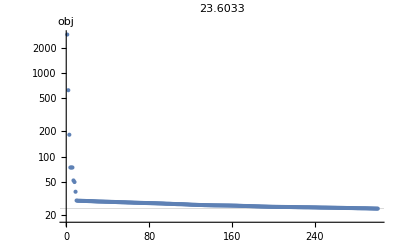

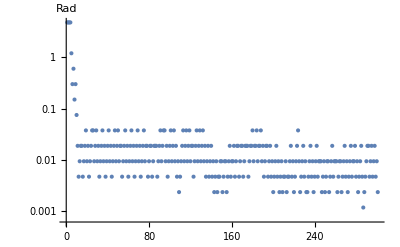

```mathematica
i=0;
MaxIter=300;
Quiet[Reap[Hmm=NestList[QNUpdate[Rosen[a],dRosen[a],ddRosen[a],STag,HTag],QNState0,MaxIter];]];
ListLogPlot[Hmm⟦All,2⟧,PlotLabel->Hmm⟦-1,2⟧,AxesLabel->"obj",GridLines->{None,{Hmm⟦-1,2⟧}}]
ListLogPlot[Hmm⟦All,6⟧,AxesLabel->"Rad",GridLines->Automatic]
```

{{-1,11},{1,289}}

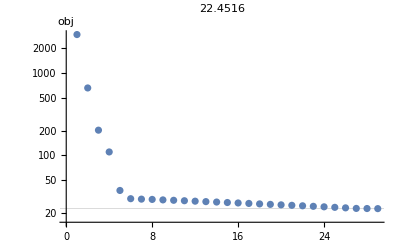

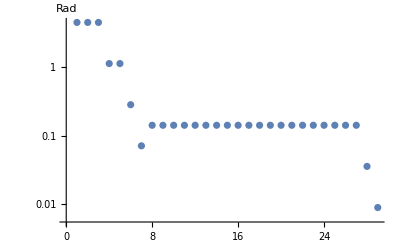

```mathematica
x0=RandomReal[{-1,1},300];
a=2;
Tally[Sign[Sort[Quiet[Eigenvalues[ddRosen[a][x0]]]]]]
```

Looking for tacking in high dimensions. x is the first direction in the “structure”.

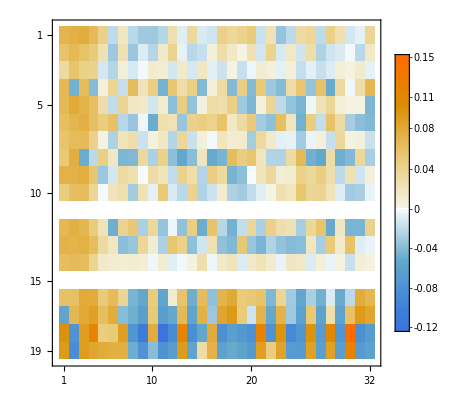

```mathematica
MatrixPlot[Table[
Hmm⟦i,1⟧-Hmm⟦i-1,1⟧,
{i,-1,-19,-1}]]
```

```mathematica
VisDims={1,2,3};
pts=Hmm[[All,1,VisDims]];
Show[
Graphics3D[Arrow[pts]],
ListPointPlot3D[pts],
Axes->True,
AxesLabel->{"a","b","c"}
]
```

-Graphics3D-

```mathematica
{x1,f1,g1,h1,H1,Δ1,S1,Y1} = Hmm⟦-1⟧;
{x2,f2,g2,h2,H2,Δ2,S2,Y2} = Hmm⟦-2⟧;
{x3,f3,g3,h3,H3,Δ3,S3,Y3} = Hmm⟦-3⟧;
TabView[{
"HStallBack2"->MatrixPlot[H3],
"JStallBack2^-1"->MatrixPlot[Inverse[ddRosen[x3]]],
"HStallBack"->MatrixPlot[H2],
"JStallBack^-1"->MatrixPlot[Inverse[ddRosen[x2]]],
"HStall"->MatrixPlot[H1],
"JStall^-1"->MatrixPlot[Inverse[ddRosen[x1]]]
}]
```

123456

```mathematica
{x
```

```mathematica
Hmm⟦All,2⟧
```

{2955.02,661.247,202.49,109.978,37.355,29.6613,29.2999,29.0685,28.681,28.3641,28.0159,27.6671,27.3264,27.0049,26.6513,26.315,25.9795,25.6379,25.2984,24.9624,24.6391,24.3078,23.9569,23.6196,23.2796,22.9418,22.5847,22.5177,22.4516}

```mathematica
TableForm[
Table[
xTest=Hmm⟦-i,1⟧,
{i,1,10}]]

TableForm[
Table[
xTest=Hmm⟦-i,1⟧;
Quiet[1/Eigenvalues[ddRosen[xTest]]]⟦-5;;-1⟧,
{i,1,10}]]
TableForm[
Table[
H=Hmm⟦-i,5⟧;
Quiet[Eigenvalues[H]⟦-5;;-1⟧],
{i,1,10}]]
```

0.354166 | 0.128375 | 0.0235901 | 0.0113348 | 0.0107801 | 0.00570228 | 0.00815068 | 0.0107317 | 0.0117867 | 0.00721035 | 0.00652466 | 0.0127263 | 0.013139 | 0.0144053 | 0.0125101 | 0.0132716 | 0.0129286 | 0.0114253 | 0.00946707 | 0.0133422 | 0.00804897 | 0.00772011 | 0.0127734 | 0.00825671 | 0.0103046 | 0.00767988 | 0.013259 | 0.0106091 | 0.00847048 | 0.00430211 | 0.0104809 | -0.00323
0.339003 | 0.128086 | 0.0221356 | 0.00925127 | 0.0144406 | 0.00977284 | 0.00947505 | 0.00862398 | 0.00381233 | 0.0158811 | 0.0125741 | 0.0104573 | 0.00824295 | 0.0138417 | 0.0140947 | 0.00485205 | 0.00951117 | 0.00653032 | 0.0102008 | 0.00736282 | 0.0169592 | 0.0103407 | 0.0113919 | 0.0156381 | 0.0143132 | 0.00914741 | 0.00719782 | 0.0103834 | 0.00270273 | 0.0135936 | 0.00883261 | -0.00333019
0.317967 | 0.109733 | 0.0200047 | 0.00863726 | 0.0104317 | 0.010118 | 0.0104177 | 0.00896758 | 0.00644825 | 0.011143 | 0.0132625 | 0.0107294 | 0.00993531 | 0.0114256 | 0.0115786 | 0.00874808 | 0.00947079 | 0.00760552 | 0.00836832 | 0.00993042 | 0.0135325 | 0.0117524 | 0.0107944 | 0.0126379 | 0.0107864 | 0.0100296 | 0.0081683 | 0.00981822 | 0.00705763 | 0.0132224 | 0.00975464 | 0.000203129
0.306065 | 0.100607 | 0.0187841 | 0.00904779 | 0.00990255 | 0.0108993 | 0.0105677 | 0.00946076 | 0.00744606 | 0.0107412 | 0.0127877 | 0.0105952 | 0.00971198 | 0.01053 | 0.0106964 | 0.00923512 | 0.00959207 | 0.00819539 | 0.00872829 | 0.00976513 | 0.0126673 | 0.0116174 | 0.0103571 | 0.0119672 | 0.0106595 | 0.0103599 | 0.00865155 | 0.00994558 | 0.00837455 | 0.0128607 | 0.0101442 | 0.000798908
0.300954 | 0.0966786 | 0.0191645 | 0.00819535 | 0.00966074 | 0.0118261 | 0.0112224 | 0.00937863 | 0.00647688 | 0.0108961 | 0.013657 | 0.0108721 | 0.00860712 | 0.0105147 | 0.0106333 | 0.00932695 | 0.00947292 | 0.00729506 | 0.0080932 | 0.0100296 | 0.0132793 | 0.0129645 | 0.00984541 | 0.0124413 | 0.0112794 | 0.0093848 | 0.00775574 | 0.0100788 | 0.00745344 | 0.0147111 | 0.00956306 | 0.00197113
0.295574 | 0.09154 | 0.019483 | 0.00778497 | 0.00961006 | 0.0120671 | 0.0115111 | 0.00955322 | 0.00643173 | 0.0107692 | 0.0137426 | 0.0107893 | 0.00798195 | 0.010566 | 0.0104746 | 0.00962152 | 0.00981195 | 0.00708641 | 0.00827551 | 0.0100204 | 0.0129969 | 0.0132808 | 0.00934402 | 0.0125437 | 0.0113314 | 0.00900613 | 0.0079431 | 0.0101947 | 0.00704007 | 0.0155288 | 0.00878257 | 0.00252395
0.28197 | 0.0821688 | 0.0188573 | 0.0102807 | 0.0098286 | 0.00887402 | 0.0104441 | 0.0131922 | 0.0146397 | 0.00803323 | 0.00458401 | 0.0114957 | 0.00672663 | 0.0095898 | 0.00738284 | 0.0113679 | 0.0139792 | 0.0101136 | 0.0124058 | 0.0106866 | 0.00622865 | 0.00775066 | 0.0108764 | 0.00960964 | 0.00853057 | 0.00867602 | 0.017231 | 0.00617035 | 0.0132193 | 0.00353453 | 0.0131475 | -0.00209776
0.256018 | 0.0706534 | 0.0159134 | 0.0105854 | 0.0102145 | 0.00991407 | 0.0102157 | 0.0116541 | 0.0113084 | 0.00958912 | 0.00871722 | 0.0107332 | 0.00865518 | 0.0102727 | 0.00902882 | 0.0106027 | 0.0119145 | 0.0102762 | 0.0109885 | 0.0102934 | 0.00898116 | 0.00914546 | 0.0100921 | 0.0103552 | 0.0100095 | 0.00969619 | 0.012262 | 0.00859238 | 0.0110711 | 0.00800635 | 0.0105935 | -0.000225577
0.25091 | 0.0647651 | 0.0130366 | 0.0141638 | 0.0110426 | 0.00491234 | 0.00806086 | 0.0120219 | 0.0110106 | 0.0108446 | 0.00881909 | 0.010491 | 0.0112643 | 0.00710929 | 0.00770358 | 0.0103839 | 0.0113711 | 0.014929 | 0.0108948 | 0.00890364 | 0.00854918 | 0.00623992 | 0.012022 | 0.00574306 | 0.0138471 | 0.0104505 | 0.0119377 | 0.010062 | 0.0124893 | 0.00589487 | 0.0109454 | -0.00484468
0.249349 | 0.0616415 | 0.0120609 | 0.0158097 | 0.0114066 | 0.00222399 | 0.00682539 | 0.0125913 | 0.0112351 | 0.0110831 | 0.00880487 | 0.0106411 | 0.0124001 | 0.00526134 | 0.00724801 | 0.0105617 | 0.0113912 | 0.0173624 | 0.0106594 | 0.00852871 | 0.008279 | 0.00436335 | 0.0131908 | 0.00334263 | 0.0154652 | 0.0105523 | 0.0121491 | 0.0104065 | 0.0134754 | 0.00442512 | 0.0112641 | -0.00727684

0.00525184 | 0.00528717 | 0.00534418 | 0.00548364 | 4.81776
0.00527468 | 0.00529387 | 0.00533309 | 0.00550386 | -0.431279
0.00524724 | 0.00528118 | 0.00529768 | 0.00544749 | -0.727689
0.00524662 | 0.00527151 | 0.00528609 | 0.00542869 | -1.03379
0.00524615 | 0.00527355 | 0.00529867 | 0.00541834 | -1.18836
0.00524932 | 0.00527058 | 0.00529651 | 0.00540701 | -2.50935
0.00527708 | 0.00528786 | 0.00528952 | 0.00541044 | 1689.67
0.00525839 | 0.00526488 | 0.00526994 | 0.00538241 | -1.8638
0.00526067 | 0.00527925 | 0.00529338 | 0.00537226 | 1.44892
0.00526549 | 0.00528999 | 0.00531292 | 0.00536769 | 0.672781

0.0041892 | 0.00391133 | 0.00366647 | 0.00314146 | -0.0016376
0.00423718 | 0.00408516 | 0.00380215 | 0.00363399 | 0.00312698
0.00419033 | 0.00389884 | 0.00374106 | 0.00336527 | 0.00316817
0.00410643 | 0.00387265 | 0.00368072 | 0.00327705 | 0.00311734
0.00384371 | 0.0036035 | 0.00326421 | 0.00313755 | -0.00311567
0.00374142 | 0.00335236 | 0.00313116 | 0.00296787 | -0.00155851
0.00367537 | 0.00327122 | 0.00294104 | 0.00287343 | -0.0019883
0.00372351 | 0.00324667 | 0.00314728 | 0.00279592 | 0.00249658
-0.00316842 | 0.00313745 | 0.00298686 | 0.00256772 | 0.00246584
0.00299569 | 0.00259917 | 0.00245445 | 0.0023681 | -0.00207172

Eigenvalues::arh: Because finding 123 out of the 123 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

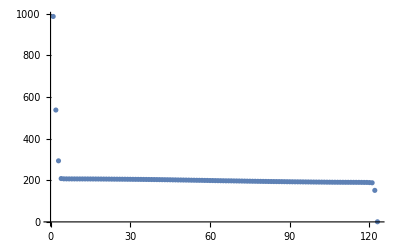

```mathematica
ListPlot[ Eigenvalues[ddRosen[Hmm⟦-1,1⟧]],PlotRange->All]
```